# Reference papers

## Perturbative Gadgets at Arbitrary Orders

## Stephen P. Jordan and Edward Farhi

https : // homepage.cem.itesm.mx/lgomez/quantum/
https://homepage.cem.itesm.mx/lgomez/quantum/menucomputing.html

```mathematica
Needs["Quantum`Computing`"]
```

Quantum`Computing` 
A Mathematica package for Quantum Computing in Dirac bra-ket notation and plotting of quantum circuits
by José Luis Gómez-Muñoz

This add-on does NOT work properly with the debugger turned on. Therefore the debugger must NOT be checked in the Evaluation menu of Mathematica.
Execute SetComputingAliases[] in order to use the keyboard to enter quantum objects in Dirac's notation
SetComputingAliases[] must be executed again in each new notebook that is created

MATHEMATICA 12.1.0 for Microsoft Windows (64-bit) (March 18, 2020)

QUANTUM version EN CONSTRUCCION

TODAY IS Fri 10 Jun 2022 16:32:56

```mathematica
SetComputingAliases[];
```

```mathematica
SetQuantumGate[A,1,Function[{q},Function[{a,b,c},a|Subscript[0, q̂]⟩·⟨Subscript[0, q̂]|+b|Subscript[0, q̂]⟩·⟨Subscript[1, q̂]|+b*|Subscript[1, q̂]⟩·⟨Subscript[0, q̂]|+c|Subscript[1, q̂]⟩·⟨Subscript[1, q̂]|]]];
Anticommutator[A_,B_]:=QuantumMatrixForm[A·B+B·A]
```

## Exploring the spectrum of different Pauli linear combinations

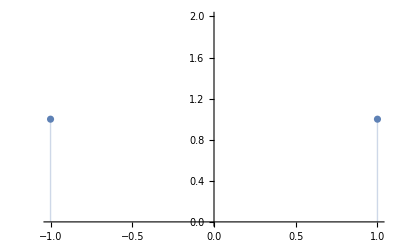

```mathematica
{e,v}=QuantumEigensystem[Subscript[𝒳, OverHat[1]]];
ListPlot[Counts[e],Filling->Axis]
```

```mathematica
a=1;b=ⅈ;c=-1;
Anticommutator[Subscript[𝒳, OverHat[1]],Subscript[A, OverHat[1]][a,b,c]]
```

ArrayFlatten::depth: The ArrayDepth of the expression at position 1 of ArrayFlatten[0] must be at least equal to the specified rank 2. (The rank is given by the optional second argument, which defaults to 2.)

ArrayFlatten[0]

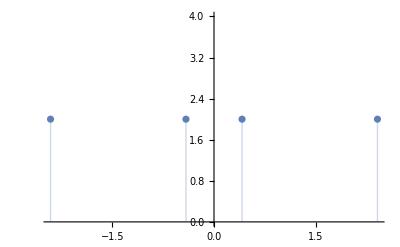

```mathematica
H=⊗_(j=1)^2 Subscript[𝒳, ĵ]+⊗_(j=1)^2 Subscript[𝒵, ĵ]+Subscript[𝒳, OverHat[1]]⊗Subscript[𝒴, OverHat[2]]⊗Subscript[𝒵, OverHat[3]];
{e,v}=QuantumEigensystem[H];
ListPlot[Counts[e],Filling->Axis]
```

```mathematica
Anticommutator[H,Subscript[A, OverHat[1]][1,0,-1]⊗Subscript[A, OverHat[2]][0,1,0]]
```

(0 | 0 | 0 | 0 | 2 ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ
-2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -2 ⅈ | 0 | 0 | 0 | 0)

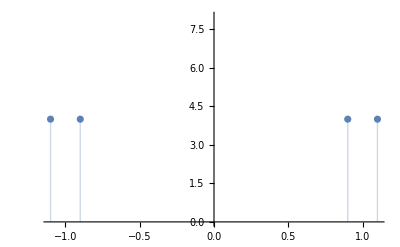

```mathematica
H=Subscript[𝒳, OverHat[1]]⊗Subscript[𝒴, OverHat[2]]⊗Subscript[𝒵, OverHat[3]]+0.1*Subscript[𝒵, OverHat[1]]⊗Subscript[𝒴, OverHat[3]]⊗Subscript[𝒵, OverHat[4]];
{e,v}=QuantumEigensystem[H];
ListPlot[Counts[Round[e,0.01]],Filling->Axis]
```

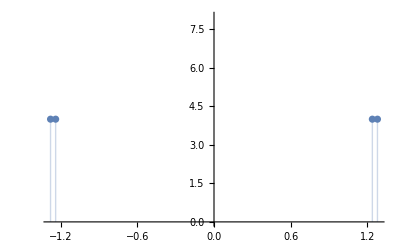

```mathematica
H=0.3*Subscript[𝒳, OverHat[1]]⊗Subscript[𝒴, OverHat[2]]⊗Subscript[𝒵, OverHat[3]]⊗Subscript[𝒵, OverHat[4]]+0.1*Subscript[𝒵, OverHat[1]]⊗Subscript[𝒴, OverHat[3]]⊗Subscript[𝒵, OverHat[4]]-0.7*Subscript[𝒴, OverHat[1]]+Subscript[𝒳, OverHat[1]]⊗Subscript[𝒳, OverHat[2]]⊗Subscript[𝒳, OverHat[3]]⊗Subscript[𝒳, OverHat[4]];
{e,v}=QuantumEigensystem[H];
ListPlot[Counts[Round[e,0.01]],Filling->Axis]
```

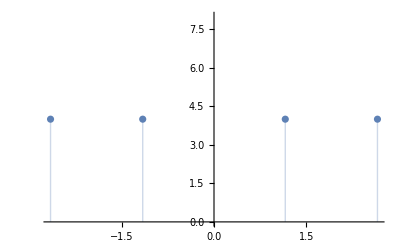

```mathematica
H=1.3*Subscript[𝒳, OverHat[1]]⊗Subscript[𝒴, OverHat[2]]⊗Subscript[𝒵, OverHat[3]]⊗Subscript[𝒵, OverHat[4]]+1.1*Subscript[𝒵, OverHat[1]]⊗Subscript[𝒴, OverHat[3]]⊗Subscript[𝒵, OverHat[4]]-0.7*Subscript[𝒴, OverHat[1]]+0.9*Subscript[𝒳, OverHat[1]]⊗Subscript[𝒳, OverHat[2]]⊗Subscript[𝒳, OverHat[3]]⊗Subscript[𝒳, OverHat[4]];
{e,v}=QuantumEigensystem[H];
ListPlot[Counts[Round[e,0.01]],Filling->Axis]
```

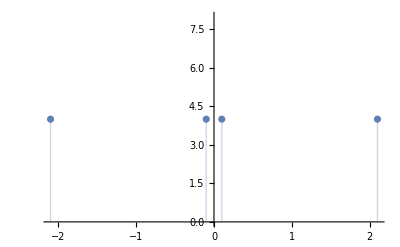

```mathematica
H=Subscript[𝒳, OverHat[1]]⊗Subscript[𝒴, OverHat[2]]⊗Subscript[𝒵, OverHat[3]]+1.1*Subscript[𝒵, OverHat[1]]⊗Subscript[𝒴, OverHat[3]]⊗Subscript[𝒵, OverHat[4]];
{e,v}=QuantumEigensystem[H];
ListPlot[Counts[Round[e,0.01]],Filling->Axis]
```

## Building a counter - example

### With different Pauli weights

(0 | 0 | 0 | 0
0 | 5 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -3)

Eigenvalue | Eigenvector
5 | |01⟩
-3 | |11⟩
0 | |10⟩
0 | |00⟩

(-1/2 | 0 | 0 | 0
0 | 9/2 | 0 | 0
0 | 0 | -1/2 | 0
0 | 0 | 0 | -7/2)

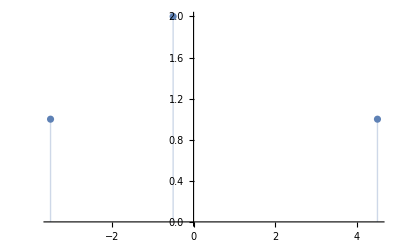

```mathematica
H:=5*(1/4)*(Subscript[ℐ, OverHat[1]]+Subscript[𝒵, OverHat[1]])⊗(Subscript[ℐ, OverHat[2]]-Subscript[𝒵, OverHat[2]])-3*(1/4)*(Subscript[ℐ, OverHat[1]]-Subscript[𝒵, OverHat[1]])⊗(Subscript[ℐ, OverHat[2]]-Subscript[𝒵, OverHat[2]])
P:=-(1/2)*Subscript[ℐ, OverHat[1]]⊗Subscript[𝒵, OverHat[2]]+2*Subscript[𝒵, OverHat[1]]⊗Subscript[ℐ, OverHat[2]]-2*Subscript[𝒵, {OverHat[1],OverHat[2]}]
QuantumMatrixForm[H]
TraditionalForm[Simplify[QuantumEigensystemForm[H]]]
QuantumMatrixForm[P]
{e,v}=QuantumEigensystem[P];
ListPlot[Counts[Round[e,0.01]],Filling->Axis]
```

### With same Pauli weights

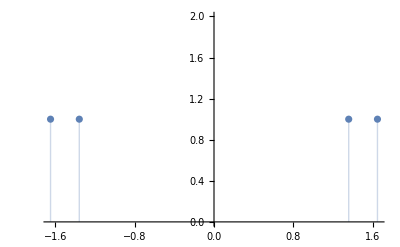

Eigenvalue | Eigenvector
1.64856 | (0.640349+0.0192481 ⅈ) |00⟩-(0.238492-0.180843 ⅈ) |01⟩+(0.232951+0.187927 ⅈ) |10⟩+0.640638 |11⟩
-1.64856 | (0.0763825+0.37006 ⅈ) |00⟩+(0.313794-0.50868 ⅈ) |10⟩+(0.274852+0.259297 ⅈ) |11⟩+0.59768 |01⟩
1.35855 | (0.101581+0.435912 ⅈ) |01⟩+(0.30008+0.332098 ⅈ) |10⟩+(0.312274-0.449608 ⅈ) |11⟩+0.547414 |00⟩
-1.35855 | -(0.339288+0.326916 ⅈ) |01⟩-(0.282435+0.377122 ⅈ) |10⟩+(0.0652235-0.523216 ⅈ) |11⟩+0.527266 |00⟩

```mathematica
P:=+0.9692 Subscript[𝒳, OverHat[1]]⊗Subscript[𝒵, OverHat[2]]+0.4795*Subscript[𝒵, {OverHat[1],OverHat[2]}]+0.9857*Subscript[𝒴, OverHat[1]]⊗Subscript[𝒵, OverHat[2]]+0.5509*Subscript[𝒳, {OverHat[1],OverHat[2]}]+0.6873*Subscript[𝒴, OverHat[1]]⊗Subscript[𝒳, OverHat[2]]+0.7969*Subscript[𝒳, OverHat[1]]⊗Subscript[𝒴, OverHat[1]]
{e,v}=QuantumEigensystem[P];
ListPlot[Counts[e],Filling->Axis]
TraditionalForm[Simplify[QuantumEigensystemForm[P]]]
```

```mathematica
P=+0.3408*Subscript[𝒵, OverHat[0]]⊗Subscript[𝒴, OverHat[1]]⊗Subscript[𝒴, OverHat[2]]⊗Subscript[𝒳, OverHat[3]] + 0.8292*Subscript[𝒳, OverHat[0]]⊗Subscript[𝒴, OverHat[1]]⊗Subscript[𝒳, OverHat[2]]⊗Subscript[𝒴, OverHat[3]] + 0.8588*Subscript[𝒳, OverHat[0]]⊗Subscript[𝒵, OverHat[1]]⊗Subscript[𝒳, OverHat[2]]⊗Subscript[𝒴, OverHat[3]]+ 0.1153*Subscript[𝒳, OverHat[0]]⊗Subscript[𝒳, OverHat[1]]⊗Subscript[𝒵, OverHat[2]]⊗Subscript[𝒳, OverHat[3]] + 0.4606*Subscript[𝒵, OverHat[0]]⊗Subscript[𝒴, OverHat[1]]⊗Subscript[𝒳, OverHat[2]]⊗Subscript[𝒴, OverHat[3]] + 0.2942*Subscript[𝒴, OverHat[0]]⊗Subscript[𝒳, OverHat[1]]⊗Subscript[𝒴, OverHat[2]]⊗Subscript[𝒵, OverHat[3]] + 0.8334*Subscript[𝒴, OverHat[0]]⊗Subscript[𝒵, OverHat[1]]⊗Subscript[𝒵, OverHat[2]]⊗Subscript[𝒳, OverHat[3]] + 0.8144*Subscript[𝒴, OverHat[0]]⊗Subscript[𝒴, OverHat[1]]⊗Subscript[𝒴, OverHat[2]]⊗Subscript[𝒵, OverHat[3]];
```

```mathematica
TeXForm[P]
```

0.3408 \mathcal{Z}_0\mathcal{Y}_1\mathcal{Y}_2\mathcal{X}_3+0.8334 \mathcal{Y}_0\mathcal{Z}_1\mathcal{Z}_2\mathcal{X}_3+0.4606
   \mathcal{Z}_0\mathcal{Y}_1\mathcal{X}_2\mathcal{Y}_3+0.8588 \mathcal{X}_0\mathcal{Z}_1\mathcal{X}_2\mathcal{Y}_3+0.2942
   \mathcal{Y}_0\mathcal{X}_1\mathcal{Y}_2\mathcal{Z}_3+0.8292 \mathcal{X}_0\mathcal{Y}_1\mathcal{X}_2\mathcal{Y}_3+0.1153
   \mathcal{X}_0\mathcal{X}_1\mathcal{Z}_2\mathcal{X}_3+0.8144 \mathcal{Y}_0\mathcal{Y}_1\mathcal{Y}_2\mathcal{Z}_3

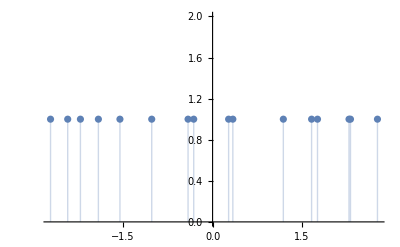

Eigenvalue | Eigenvector
2.76795 | -(0.0268358-0.276652 ⅈ) |0001⟩+(0.276652+0.0268358 ⅈ) |0010⟩-(0.0230095+0.213399 ⅈ) |0011⟩-(0.0186171+0.339166 ⅈ) |0100⟩+(0.0685899-0.0811798 ⅈ) |0101⟩-(0.0811798+0.0685899 ⅈ) |0110⟩+(0.339166-0.0186171 ⅈ) |0111⟩-(0.339208-0.0178495 ⅈ) |1000⟩-(0.073359-0.0768973 ⅈ) |1001⟩+(0.0768973+0.073359 ⅈ) |1010⟩-(0.0178495+0.339208 ⅈ) |1011⟩+(0.+0.214636 ⅈ) |1100⟩-(0.27218-0.0563388 ⅈ) |1101⟩+(0.0563388+0.27218 ⅈ) |1110⟩+(-0.213399+0.0230095 ⅈ) |0000⟩-0.214636 |1111⟩
-2.72039 | (0.350775-0.00740006 ⅈ) |0000⟩-(0.079729-0.101603 ⅈ) |0001⟩+(0.101603+0.079729 ⅈ) |0010⟩+(0.00740006+0.350775 ⅈ) |0011⟩+(0.00700533-0.195975 ⅈ) |0100⟩-(0.264546-0.0422212 ⅈ) |0101⟩+(0.0422212+0.264546 ⅈ) |0110⟩+(0.195975+0.00700533 ⅈ) |0111⟩-(0.195783-0.0111372 ⅈ) |1000⟩+(0.0366321-0.265378 ⅈ) |1001⟩-(0.265378+0.0366321 ⅈ) |1010⟩-(0.0111372+0.195783 ⅈ) |1011⟩-(0.+0.350853 ⅈ) |1100⟩-(0.0998989-0.0818543 ⅈ) |1101⟩+(0.0818543+0.0998989 ⅈ) |1110⟩+0.350853 |1111⟩
-2.43222 | -(0.0702034+0.0232771 ⅈ) |0001⟩+(0.0232771-0.0702034 ⅈ) |0010⟩-(0.103031-0.212896 ⅈ) |0011⟩+(0.132161-0.343395 ⅈ) |0100⟩+(0.190373-0.130235 ⅈ) |0101⟩+(0.130235+0.190373 ⅈ) |0110⟩-(0.343395+0.132161 ⅈ) |0111⟩-(0.366672+0.030627 ⅈ) |1000⟩-(0.200159-0.114627 ⅈ) |1001⟩-(0.114627+0.200159 ⅈ) |1010⟩-(0.030627-0.366672 ⅈ) |1011⟩+(0.+0.236517 ⅈ) |1100⟩-(0.00962943-0.0733323 ⅈ) |1101⟩-(0.0733323+0.00962943 ⅈ) |1110⟩+(-0.212896-0.103031 ⅈ) |0000⟩+0.236517 |1111⟩
2.31494 | (0.14902-0.168217 ⅈ) |0001⟩+(0.168217+0.14902 ⅈ) |0010⟩+(0.0799997+0.350174 ⅈ) |0011⟩+(0.0842531+0.238768 ⅈ) |0100⟩+(0.0323057-0.0729472 ⅈ) |0101⟩+(0.0729472+0.0323057 ⅈ) |0110⟩+(0.238768-0.0842531 ⅈ) |0111⟩+(0.251536+0.0289588 ⅈ) |1000⟩-(0.0639199-0.0477409 ⅈ) |1001⟩-(0.0477409+0.0639199 ⅈ) |1010⟩+(0.0289588-0.251536 ⅈ) |1011⟩+(0.+0.359196 ⅈ) |1100⟩+(0.130802-0.182742 ⅈ) |1101⟩+(0.182742+0.130802 ⅈ) |1110⟩+(-0.350174+0.0799997 ⅈ) |0000⟩+0.359196 |1111⟩
2.29037 | (0.319849-0.0249634 ⅈ) |0000⟩-(0.0873934-0.18988 ⅈ) |0001⟩+(0.18988+0.0873934 ⅈ) |0010⟩+(0.0249634+0.319849 ⅈ) |0011⟩+(0.0151088-0.0305623 ⅈ) |0100⟩-(0.317455-0.0379649 ⅈ) |0101⟩+(0.0379649+0.317455 ⅈ) |0110⟩+(0.0305623+0.0151088 ⅈ) |0111⟩+(0.029294-0.017441 ⅈ) |1000⟩-(0.0131483-0.319447 ⅈ) |1001⟩+(0.319447+0.0131483 ⅈ) |1010⟩+(0.017441+0.029294 ⅈ) |1011⟩+(0.+0.320822 ⅈ) |1100⟩+(0.182504-0.101903 ⅈ) |1101⟩-(0.101903+0.182504 ⅈ) |1110⟩-0.320822 |1111⟩
-2.21871 | (0.0621448-0.0341354 ⅈ) |0000⟩-(0.0516841+0.336421 ⅈ) |0001⟩-(0.336421-0.0516841 ⅈ) |0010⟩+(0.0341354+0.0621448 ⅈ) |0011⟩+(0.069215+0.299042 ⅈ) |0100⟩-(0.13053-0.133671 ⅈ) |0101⟩+(0.133671+0.13053 ⅈ) |0110⟩-(0.299042-0.069215 ⅈ) |0111⟩-(0.295427-0.083305 ⅈ) |1000⟩-(0.0543179-0.178761 ⅈ) |1001⟩+(0.178761+0.0543179 ⅈ) |1010⟩-(0.083305+0.295427 ⅈ) |1011⟩+(0.+0.0709028 ⅈ) |1100⟩-(0.319748-0.116666 ⅈ) |1101⟩+(0.116666+0.319748 ⅈ) |1110⟩-0.0709028 |1111⟩
-1.91707 | (0.160829+0.160693 ⅈ) |0000⟩-(0.0169978+0.128698 ⅈ) |0001⟩+(0.128698-0.0169978 ⅈ) |0010⟩+(0.160693-0.160829 ⅈ) |0011⟩-(0.201356-0.088416 ⅈ) |0100⟩+(0.359026+0.0647977 ⅈ) |0101⟩-(0.0647977-0.359026 ⅈ) |0110⟩+(0.088416+0.201356 ⅈ) |0111⟩-(0.204866-0.0799477 ⅈ) |1000⟩+(0.207923-0.299776 ⅈ) |1001⟩+(0.299776+0.207923 ⅈ) |1010⟩+(0.0799477+0.204866 ⅈ) |1011⟩+(0.+0.22735 ⅈ) |1100⟩-(0.0790279+0.102989 ⅈ) |1101⟩+(0.102989-0.0790279 ⅈ) |1110⟩+0.22735 |1111⟩
1.76129 | (0.112733+0.162691 ⅈ) |0000⟩+(0.260102+0.167754 ⅈ) |0001⟩-(0.167754-0.260102 ⅈ) |0010⟩+(0.162691-0.112733 ⅈ) |0011⟩+(0.280121+0.0826535 ⅈ) |0100⟩+(0.166275+0.0456236 ⅈ) |0101⟩-(0.0456236-0.166275 ⅈ) |0110⟩+(0.0826535-0.280121 ⅈ) |0111⟩-(0.183171-0.227481 ⅈ) |1000⟩-(0.110685-0.132203 ⅈ) |1001⟩-(0.132203+0.110685 ⅈ) |1010⟩+(0.227481+0.183171 ⅈ) |1011⟩-(0.+0.197932 ⅈ) |1100⟩+(0.118248-0.286029 ⅈ) |1101⟩+(0.286029+0.118248 ⅈ) |1110⟩-0.197932 |1111⟩
1.66221 | (0.0858451+0.107887 ⅈ) |0000⟩+(0.221396-0.126739 ⅈ) |0001⟩+(0.126739+0.221396 ⅈ) |0010⟩+(0.107887-0.0858451 ⅈ) |0011⟩-(0.145551-0.0160933 ⅈ) |0100⟩-(0.278502-0.258659 ⅈ) |0101⟩-(0.258659+0.278502 ⅈ) |0110⟩+(0.0160933+0.145551 ⅈ) |0111⟩-(0.123915-0.0780326 ⅈ) |1000⟩-(0.378982+0.0289965 ⅈ) |1001⟩+(0.0289965-0.378982 ⅈ) |1010⟩+(0.0780326+0.123915 ⅈ) |1011⟩+(0.+0.137873 ⅈ) |1100⟩-(0.252157-0.0386753 ⅈ) |1101⟩-(0.0386753+0.252157 ⅈ) |1110⟩+0.137873 |1111⟩
-1.55528 | (0.0997293-0.17722 ⅈ) |0000⟩-(0.292002-0.289422 ⅈ) |0001⟩-(0.289422+0.292002 ⅈ) |0010⟩-(0.17722+0.0997293 ⅈ) |0011⟩-(0.107894+0.0395131 ⅈ) |0100⟩+(0.00274161+0.162502 ⅈ) |0101⟩-(0.162502-0.00274161 ⅈ) |0110⟩-(0.0395131-0.107894 ⅈ) |0111⟩+(0.113407+0.0184787 ⅈ) |1000⟩-(0.0820836-0.140273 ⅈ) |1001⟩-(0.140273+0.0820836 ⅈ) |1010⟩+(0.0184787-0.113407 ⅈ) |1011⟩+(0.+0.203354 ⅈ) |1100⟩-(0.112537+0.395431 ⅈ) |1101⟩+(0.395431-0.112537 ⅈ) |1110⟩+0.203354 |1111⟩
1.18779 | (0.0743375+0.0289875 ⅈ) |0001⟩-(0.0289875-0.0743375 ⅈ) |0010⟩+(0.173631+0.02058 ⅈ) |0011⟩-(0.25517+0.212154 ⅈ) |0100⟩+(0.320659-0.0109259 ⅈ) |0101⟩+(0.0109259+0.320659 ⅈ) |0110⟩-(0.212154-0.25517 ⅈ) |0111⟩+(0.278367-0.180644 ⅈ) |1000⟩-(0.317144+0.0485927 ⅈ) |1001⟩+(0.0485927-0.317144 ⅈ) |1010⟩-(0.180644+0.278367 ⅈ) |1011⟩-(0.+0.174846 ⅈ) |1100⟩+(0.0772327-0.0200362 ⅈ) |1101⟩+(0.0200362+0.0772327 ⅈ) |1110⟩+(-0.02058+0.173631 ⅈ) |0000⟩-0.174846 |1111⟩
-1.02167 | (0.345652+0.11732 ⅈ) |0000⟩+(0.165133+0.252258 ⅈ) |0001⟩-(0.252258-0.165133 ⅈ) |0010⟩+(0.11732-0.345652 ⅈ) |0011⟩+(0.101623-0.108393 ⅈ) |0100⟩-(0.0313333+0.0529121 ⅈ) |0101⟩+(0.0529121-0.0313333 ⅈ) |0110⟩-(0.108393+0.101623 ⅈ) |0111⟩+(0.135304-0.061393 ⅈ) |1000⟩+(0.0400339+0.0466771 ⅈ) |1001⟩-(0.0466771-0.0400339 ⅈ) |1010⟩-(0.061393+0.135304 ⅈ) |1011⟩+(0.+0.365019 ⅈ) |1100⟩+(0.185799+0.237449 ⅈ) |1101⟩-(0.237449-0.185799 ⅈ) |1110⟩+0.365019 |1111⟩
-0.411766 | (0.0011417+0.260509 ⅈ) |0001⟩+(0.260509-0.0011417 ⅈ) |0010⟩-(0.100612+0.277239 ⅈ) |0011⟩+(0.0835908+0.24956 ⅈ) |0100⟩-(0.135516-0.0867008 ⅈ) |0101⟩+(0.0867008+0.135516 ⅈ) |0110⟩-(0.24956-0.0835908 ⅈ) |0111⟩-(0.263106-0.00655776 ⅈ) |1000⟩-(0.0352704-0.156964 ⅈ) |1001⟩+(0.156964+0.0352704 ⅈ) |1010⟩-(0.00655776+0.263106 ⅈ) |1011⟩-(0.+0.294931 ⅈ) |1100⟩+(0.245272-0.0877961 ⅈ) |1101⟩-(0.0877961+0.245272 ⅈ) |1110⟩+(-0.277239+0.100612 ⅈ) |0000⟩+0.294931 |1111⟩
0.340028 | (0.194721-0.110384 ⅈ) |0000⟩+(0.143606+0.123248 ⅈ) |0001⟩+(0.123248-0.143606 ⅈ) |0010⟩+(0.110384+0.194721 ⅈ) |0011⟩+(0.124281+0.260006 ⅈ) |0100⟩+(0.197722-0.204801 ⅈ) |0101⟩-(0.204801+0.197722 ⅈ) |0110⟩-(0.260006-0.124281 ⅈ) |0111⟩-(0.28748-0.0201061 ⅈ) |1000⟩+(0.0806573-0.273005 ⅈ) |1001⟩-(0.273005+0.0806573 ⅈ) |1010⟩-(0.0201061+0.28748 ⅈ) |1011⟩+(0.+0.223832 ⅈ) |1100⟩+(0.178039+0.0641484 ⅈ) |1101⟩+(0.0641484-0.178039 ⅈ) |1110⟩-0.223832 |1111⟩
-0.316708 | (0.035892+0.238871 ⅈ) |0001⟩+(0.238871-0.035892 ⅈ) |0010⟩-(0.114557+0.153775 ⅈ) |0011⟩+(0.122012+0.21017 ⅈ) |0100⟩-(0.275066-0.141996 ⅈ) |0101⟩+(0.141996+0.275066 ⅈ) |0110⟩-(0.21017-0.122012 ⅈ) |0111⟩+(0.241434-0.0277124 ⅈ) |1000⟩-(0.0504567+0.305415 ⅈ) |1001⟩-(0.305415-0.0504567 ⅈ) |1010⟩+(0.0277124+0.241434 ⅈ) |1011⟩+(0.+0.191756 ⅈ) |1100⟩-(0.213001-0.113922 ⅈ) |1101⟩+(0.113922+0.213001 ⅈ) |1110⟩+(-0.153775+0.114557 ⅈ) |0000⟩-0.191756 |1111⟩
0.269232 | (0.153608-0.159466 ⅈ) |0000⟩+(0.131881+0.259041 ⅈ) |0001⟩+(0.259041-0.131881 ⅈ) |0010⟩+(0.159466+0.153608 ⅈ) |0011⟩+(0.134869+0.145674 ⅈ) |0100⟩+(0.12608-0.247333 ⅈ) |0101⟩-(0.247333+0.12608 ⅈ) |0110⟩-(0.145674-0.134869 ⅈ) |0111⟩+(0.198197-0.0113496 ⅈ) |1000⟩-(0.0807841-0.2656 ⅈ) |1001⟩+(0.2656+0.0807841 ⅈ) |1010⟩+(0.0113496+0.198197 ⅈ) |1011⟩-(0.+0.221415 ⅈ) |1100⟩-(0.274693-0.095071 ⅈ) |1101⟩+(0.095071+0.274693 ⅈ) |1110⟩+0.221415 |1111⟩

```mathematica
P:=+0.3408*Subscript[𝒵, OverHat[0]]⊗Subscript[𝒴, OverHat[1]]⊗Subscript[𝒴, OverHat[2]]⊗Subscript[𝒳, OverHat[3]] + 0.8292*Subscript[𝒳, OverHat[0]]⊗Subscript[𝒴, OverHat[1]]⊗Subscript[𝒳, OverHat[2]]⊗Subscript[𝒴, OverHat[3]] + 0.8588*Subscript[𝒳, OverHat[0]]⊗Subscript[𝒵, OverHat[1]]⊗Subscript[𝒳, OverHat[2]]⊗Subscript[𝒴, OverHat[3]]+ 0.1153*Subscript[𝒳, OverHat[0]]⊗Subscript[𝒳, OverHat[1]]⊗Subscript[𝒵, OverHat[2]]⊗Subscript[𝒳, OverHat[3]] + 0.4606*Subscript[𝒵, OverHat[0]]⊗Subscript[𝒴, OverHat[1]]⊗Subscript[𝒳, OverHat[2]]⊗Subscript[𝒴, OverHat[3]] + 0.2942*Subscript[𝒴, OverHat[0]]⊗Subscript[𝒳, OverHat[1]]⊗Subscript[𝒴, OverHat[2]]⊗Subscript[𝒵, OverHat[3]] + 0.8334*Subscript[𝒴, OverHat[0]]⊗Subscript[𝒵, OverHat[1]]⊗Subscript[𝒵, OverHat[2]]⊗Subscript[𝒳, OverHat[3]] + 0.8144*Subscript[𝒴, OverHat[0]]⊗Subscript[𝒴, OverHat[1]]⊗Subscript[𝒴, OverHat[2]]⊗Subscript[𝒵, OverHat[3]]
{e,v}=QuantumEigensystem[P];
ListPlot[Counts[e],Filling->Axis]
TraditionalForm[Simplify[QuantumEigensystemForm[P]]]
```

```mathematica
Sort[e]
```

{-2.72039,-2.43222,-2.21871,-1.91707,-1.55528,-1.02167,-0.411766,-0.316708,0.269232,0.340028,1.18779,1.66221,1.76129,2.29037,2.31494,2.76795}

## Arbitrary unitary matrix

```mathematica
SetQuantumGate[A,1,Function[{q},Function[{a,b,ϕ},(1/Sqrt[Abs[a]^2+Abs[b]^2])*(a|Subscript[0, q̂]⟩·⟨Subscript[0, q̂]|+b|Subscript[0, q̂]⟩·⟨Subscript[1, q̂]|-Exp[-ⅈ*ϕ]*b*|Subscript[1, q̂]⟩·⟨Subscript[0, q̂]|+Exp[ⅈ*ϕ]*a*|Subscript[1, q̂]⟩·⟨Subscript[1, q̂]|)]]];
a=1;b=1;ϕ=0;
QuantumMatrixForm[Subscript[σ, 𝒳,OverHat[1]]·Subscript[A, OverHat[1]][a,b,ϕ]]
PauliExpand[Subscript[A, OverHat[1]][a,b,ϕ]]
⟦Subscript[σ, 𝒳,OverHat[1]],PauliExpand[Subscript[A, OverHat[1]][a,b,ϕ]]⟧_+
```

(-1/(√2) | 1/(√2)
1/(√2) | 1/(√2))

(σ_(0,OverHat[1]))/(√2)+(ⅈ σ_(𝒴,OverHat[1]))/(√2)

√2 σ_(𝒳,OverHat[1])

## Spectrum of an arbitrary Hermitian matrix

### dim = 2

```mathematica
mat=Table[Subscript[m,i,j],{i,2},{j,2}];
mat//MatrixForm
```

(m_(1,1) | m_(1,2)
m_(2,1) | m_(2,2))

```mathematica
mat⟦2,1⟧=Conjugate[mat⟦1,2⟧];
mat//MatrixForm
```

(m_(1,1) | m_(1,2)
(m_(1,2))^* | m_(2,2))

```mathematica
Simplify[Eigenvalues[mat]]
```

{1/2 (m_(1,1)+m_(2,2)-√(m_(1,1)^2+4 (m_(1,2))^* m_(1,2)-2 m_(1,1) m_(2,2)+m_(2,2)^2)),1/2 (m_(1,1)+m_(2,2)+√(m_(1,1)^2+4 (m_(1,2))^* m_(1,2)-2 m_(1,1) m_(2,2)+m_(2,2)^2))}

### dim = 4

```mathematica
mat=Table[Subscript[m,i,j],{i,4},{j,4}];
For[i=1,i<4,i++,]
mat⟦2,1⟧=Conjugate[mat⟦1,2⟧];
```

(m_(1,1) | m_(1,2) | m_(1,3) | m_(1,4)
m_(2,1) | m_(2,2) | m_(2,3) | m_(2,4)
m_(3,1) | m_(3,2) | m_(3,3) | m_(3,4)
m_(4,1) | m_(4,2) | m_(4,3) | m_(4,4))

```mathematica
mat//MatrixForm
```

(m_(1,1) | m_(1,2)
(m_(1,2))^* | m_(2,2))

```mathematica
Simplify[Eigenvalues[mat]]
```

{1/2 (m_(1,1)+m_(2,2)-√(m_(1,1)^2+4 (m_(1,2))^* m_(1,2)-2 m_(1,1) m_(2,2)+m_(2,2)^2)),1/2 (m_(1,1)+m_(2,2)+√(m_(1,1)^2+4 (m_(1,2))^* m_(1,2)-2 m_(1,1) m_(2,2)+m_(2,2)^2))}